# CoFiAM

```mathematica
Clear["Global`*"];
```

```mathematica
yy=Select[Characters[Last[StringSplit[NotebookFileName[],"/"]]],!MemberQ[Alphabet[],#]&];
yy=ToExpression[StringJoin[yy[[1;;Length[yy]-1]]]]
```

1

```mathematica
tcut1=0;
tcut2=∞;
```

### Q Initialization

Define the import folder

```mathematica
thisfolder=NotebookDirectory[];
type="NEA";
If[StringSplit[thisfolder,"/"][[Length[StringSplit[thisfolder,"/"]]-0]]=="PDC",pdc=1,pdc=0];
planetnumber=ToExpression[Last[Characters[StringSplit[thisfolder,"/"][[Length[StringSplit[thisfolder,"/"]]-1]]]]];
kic=StringSplit[thisfolder,"/"][[Length[StringSplit[thisfolder,"/"]]-2]];
temp=StringSplit[thisfolder,"/"][[1;;Length[StringSplit[thisfolder,"/"]]-2]];
j=0;datafolder="/";Label[jloop];j=j+1;datafolder=StringJoin[datafolder,temp[[j]],"/"];If[j<Length[temp],Goto[jloop]]
datafolder=StringJoin[datafolder,"RawsLC/"];
Clear[temp];
temp=StringSplit[thisfolder,"/"][[1;;Length[StringSplit[thisfolder,"/"]]-3]];
j=0;rootfolder="/";Label[jloop];j=j+1;rootfolder=StringJoin[rootfolder,temp[[j]],"/"];If[j<Length[temp],Goto[jloop]]
Clear[temp];
```

Import all of the raws....

```mathematica
files=Flatten[Import[StringJoin[datafolder,"files.txt"],"Table"]];
filesLC=Select[files,StringContainsQ[#,"_llc.dat"]&];
filesSC=Select[files,StringContainsQ[#,"_slc.dat"]&];
j=0;Label[jloop];j=j+1;Subscript[rawLC, j]=Import[StringJoin[datafolder,filesLC[[j]]],"Table"];Subscript[rawLC, j]=Select[Subscript[rawLC, j],Length[#]==6&];If[pdc==0,Subscript[rawLC, j]=Subscript[rawLC, j][[All,{1,2,3,6}]],Subscript[rawLC, j]=Subscript[rawLC, j][[All,{1,4,5,6}]]];If[j<Length[filesLC],Goto[jloop]];
j=0;Label[jloop];If[Length[filesSC]==0,Goto[endloop]];j=j+1;If[pdc==0,Subscript[rawSC, j]=Import[StringJoin[datafolder,filesSC[[j]]],"Table"][[All,{1,2,3,6}]],Subscript[rawSC, j]=Import[StringJoin[datafolder,filesSC[[j]]],"Table"][[All,{1,4,5,6}]]];If[j<Length[filesSC],Goto[jloop]];Label[endloop];
```

Import the info file

```mathematica
infofile=Import[StringJoin[rootfolder,type,".csv"],"CSV"][[19;;All]];
kic2=ToExpression[StringSplit[StringSplit[files[[1]],"-"][[1]],"lr"][[2]]];
infoline=Select[infofile,#[[1]]==kic2&][[planetnumber]]
```

{10063802,K01888.01,120.018,0.0006493,-0.0006493,134.187,0.00471,-0.00471,11.637,0.159,-0.159}

```mathematica
period=infoline[[3]]
tau0=infoline[[6]]+54833
"read duration (only for NEA, else you'll need to mannually input";
duration=N[infoline[[9]]/24]
```

120.018

54967.2

0.484875

check how many transits are in the Kepler data, and where

```mathematica
RAWLC=Sort[Flatten[Table[Subscript[rawLC, i],{i,1,Length[filesLC]}],1]];
tmin=First[RAWLC][[1]]+54833;
tmax=Last[RAWLC][[1]]+54833;
epochrange={Floor[(tmin-tau0)/period],Ceiling[(tmax-tau0)/period]};
expectedtimes=Select[Table[tau0+e period,{e,epochrange[[1]],epochrange[[2]],1}],tmin<#<tmax&];
```

get the Mazeh times

```mathematica
mazeh=Import["/Users/dkipping/Storage1/Work/Documents/Transit_Work/PAPERS/Undersampled/mazeh_analysis/ttvs.txt","Table"];
mazeh=mazeh[[47;;All]];
koiname=ToExpression[StringSplit[First[Select[StringSplit[NotebookFileName[],"/"],StringStartsQ[#,"KOI-"]&]],"-"][[2]]];
thismazeh=Select[mazeh,#[[1]]==koiname&];thismazeh=Table[thismazeh[[i,3]]+54900+thismazeh[[i,4]]/(24*60),{i,1,Length[thismazeh]}]
```

{54967.2,55087.2,55207.2,55327.2,55447.3,55687.3,55807.3,55927.3,56047.3,56167.4,56287.4,56407.4}

include other expected times

```mathematica
j=0;Label[jloop];j=j+1;If[Length[Select[thismazeh,Abs[#-expectedtimes[[j]]]<0.5period&]]==1,Subscript[α, j]=First[Nearest[thismazeh,expectedtimes[[j]]]],Subscript[α, j]=expectedtimes[[j]]];If[j<Length[expectedtimes],Goto[jloop]];
observedtimes=Table[Subscript[α, jj],{jj,1,Length[expectedtimes]}];
```

identify the quarter for each observed times

```mathematica
j=0;Label[jloop];j=j+1;Subscript[ψuarter, j]=-1;k=0;Label[kloop];k=k+1;If[Min[Subscript[rawLC, k][[All,1]]]+54833<observedtimes[[j]]<Max[Subscript[rawLC, k][[All,1]]]+54833,Subscript[ψuarter, j]=k];If[k<Length[filesLC],Goto[kloop]];If[j<Length[observedtimes],Goto[jloop]];
observedtimes2=Select[Table[{observedtimes[[jj]],Subscript[ψuarter, jj]},{jj,1,Length[observedtimes]}],#[[2]]≠-1&]
```

{{54967.2,2},{55087.2,3},{55207.2,5},{55327.2,6},{55447.3,7},{55687.3,10},{55807.3,11},{55927.3,12},{56047.3,14},{56167.4,15},{56287.4,16},{56407.4,18}}

```mathematica
numero=observedtimes2[[yy,2]]
thisraw=Subscript[rawLC, numero];
err=Select[thisraw,#[[4]]==0&][[All,{1,2,3}]];
err=Table[{err[[i,1]]+54833,err[[i,2]],err[[i,3]]},{i,1,Length[err]}];
temp=Median[Table[err[[i+1,1]]-err[[i,1]],{i,1,Length[err]-1}]]*24*60;
If[temp>10,sc=0,sc=1];
```

2

```mathematica
toff=54833;quarter=-1;
exampletime=First[Median[err]];
Q0start=54953.53841518038;Q0end=54963.24481732253;
Q1start=54964.511756673426;Q1end=54997.98329729108;
Q2start=55002.764903284085;Q2end=55091.466956257034;
Q3start=55093.24459723139;Q3end=55182.49465072287;
Q4start=55185.3658080061;Q4end=55275.211866897414;
Q5start=55276.47949780036;Q5end=55371.17207391215;
Q6start=55372.46009847967;Q6end=55462.305792973355;
Q7start=55463.16463513537;Q7end=55552.55707265549;
Q8start=55568.35242605389;Q8end=55635.35368505794;
Q9start=55641.52550915837;Q9end=55738.935875129384;
Q10start=55739.835638486584;Q10end=55833.277845301614;
Q11start=55834.1986379302;Q11end=55931.33445044336;
Q12start=55932.418064826525;Q12end=56015.03062305053;
Q13start=56015.72674011688;Q13end=56106.066162428935;
Q14start=56107.13008618061;Q14end=56204.331588511515;
Q15start=56206.50817485861;Q15end=56304.13718779086;
Q16start=56305.08740097;Q16end=56390.96969746;
If[Q0start<exampletime<Q0end,quarter=0];
If[Q1start<exampletime<Q1end,quarter=1];
If[Q2start<exampletime<Q2end,quarter=2];
If[Q3start<exampletime<Q3end,quarter=3];
If[Q4start<exampletime<Q4end,quarter=4];
If[Q5start<exampletime<Q5end,quarter=5];
If[Q6start<exampletime<Q6end,quarter=6];
If[Q7start<exampletime<Q7end,quarter=7];
If[Q8start<exampletime<Q8end,quarter=8];
If[Q9start<exampletime<Q9end,quarter=9];
If[Q10start<exampletime<Q10end,quarter=10];
If[Q11start<exampletime<Q11end,quarter=11];
If[Q12start<exampletime<Q12end,quarter=12];
If[Q13start<exampletime<Q13end,quarter=13];
If[Q14start<exampletime<Q14end,quarter=14];
If[Q15start<exampletime<Q15end,quarter=15];
If[Q16start<exampletime<Q16end,quarter=16];
If[exampletime>Q16end,quarter=17];
If[quarter==-1,Print["Error quarter unidentified"],Print["quarter ",quarter]]
If[quarter==-1,Speak["Error quarter unidentified"]]
```

quarter 1

```mathematica
Pp=period;tau0=observedtimes2[[yy,1]];
τ0=tau0
T14=duration;
Thill=T14*3;
myepoch=0
```

54967.2

0

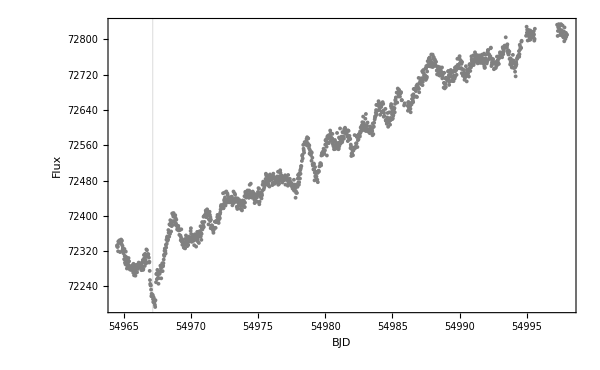

```mathematica
ListPlot[err[[All,{1,2}]],GridLines->{{observedtimes2[[yy,1]],55016},{}},Frame->True,BaseStyle->{"Times",16},FrameLabel->{"BJD","Flux"},ImageSize->{600,400},PlotStyle->{Gray},Axes->None]
```

```mathematica
If[pdc==0,err=Select[err,Max[tcut1,observedtimes2[[yy,1]]-0.5Pp]<#[[1]]<Min[tcut2,observedtimes2[[yy,1]]+0.5Pp]&],err=Select[err,observedtimes2[[yy,1]]-0.5Pp<#[[1]]<observedtimes2[[yy,1]]+0.5Pp&]];
```

Now plot, adding gridlines for the expected transits

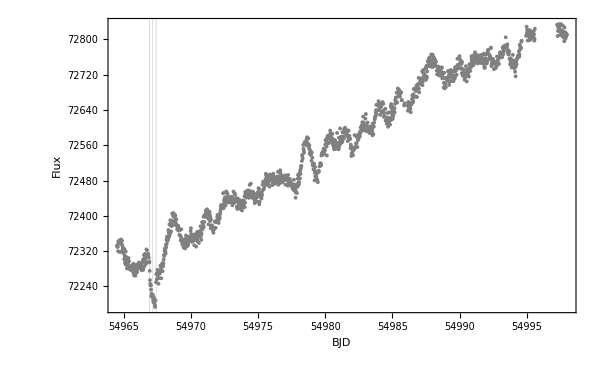

```mathematica
epoch=First[Table[Floor[(Extract[Extract[err,i],1]-τ0)/Pp],{i,1,Length[err]}]]+1;
ListPlot[err[[All,{1,2}]],GridLines->{{tau0,tau0-0.5T14,tau0+0.5T14},{}},Frame->True,BaseStyle->{"Times",16},FrameLabel->{"BJD","Flux"},ImageSize->{600,400},PlotStyle->{Gray},Axes->None]
```

Now exclude transits...

```mathematica
gap=0.5T14+N[0.5/24];
temp=err;
phase=Table[Extract[Extract[err,i],1]-Pp Floor[(Extract[Extract[err,i],1]-τ0)/Pp]-τ0,{i,1,Length[err]}];
phase=Table[(Extract[phase,i]/Pp)-Round[(Extract[phase,i]/Pp)],{i,1,Length[phase]}];
n=0;Label[nloop];n=n+1;ϕmax=gap/Pp;j=0;m=0;Label[jloop];j=j+1;If[Abs[Extract[phase,j]]>ϕmax,m=m+1];If[Abs[Extract[phase,j]]>ϕmax,Subscript[α, m]=Extract[temp,j]];If[j<Length[temp],Goto[jloop]];mmax=m;Print["For transit number ",n,", ",mmax," points out of ",Length[temp]," are accepted"];temp=Table[Subscript[α, mm],{mm,1,mmax}];If[n<1,Goto[nloop]];
out=temp;
```

For transit number 1, 1371 points out of 1396 are accepted

Now accept temp as the out-of-transits array...

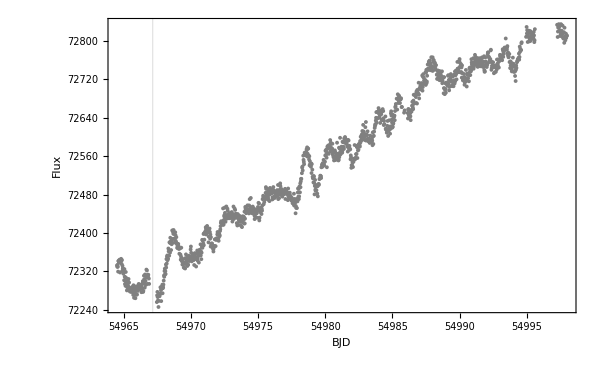

```mathematica
out=temp;
outlist=Table[{Extract[Extract[out,i],1],Extract[Extract[out,i],2]},{i,1,Length[out]}];
ListPlot[outlist,GridLines->{{τ0+epoch Pp},{}},Frame->True,BaseStyle->{"Times",16},FrameLabel->{"BJD","Flux"},ImageSize->{600,400},PlotStyle->{Gray},Axes->None]
```

### Outlier rejection for Q

Q3 is relatively simple to clean.
There are no jumps or exponential rises.
We can therefore skip straight to outlier rejection followed by cosine filter.

InterpolatingFunction::dmval: Input value {54964.5} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {54964.6} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

72256.4

72834.3

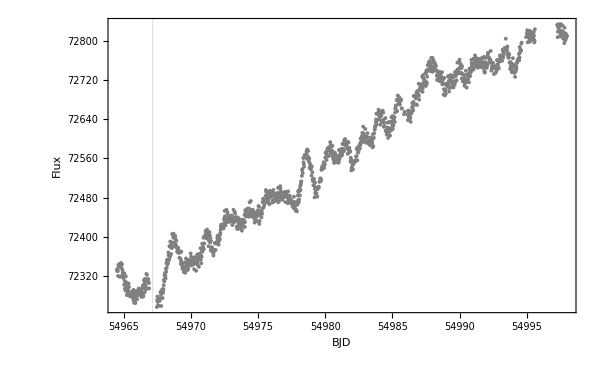

15 points removed

```mathematica
bin=20;
sigma=3;
smoothfn=Interpolation[MovingMedian[outlist,bin],InterpolationOrder->1];
res=Table[{Extract[Extract[out,i],1],Extract[Extract[out,i],2]-smoothfn[Extract[Extract[out,i],1]],Extract[Extract[out,i],3]},{i,1,Length[out]}];
j=0;m=0;Label[jloop];j=j+1;If[Abs[Extract[Extract[res,j],2]/Extract[Extract[res,j],3]]<sigma,m=m+1];If[Abs[Extract[Extract[res,j],2]/Extract[Extract[res,j],3]]<sigma,Subscript[γ, m]=Extract[out,j]];If[j<Length[res],Goto[jloop]];mmax=m;
nice=Table[Subscript[γ, mm],{mm,1,mmax}];
nicelist=Table[{Extract[Extract[nice,i],1],Extract[Extract[nice,i],2]},{i,1,Length[nice]}];
fluxmin=Last[First[Sort[nicelist,#1[[2]]<#2[[2]]&]]]
fluxmax=Last[Last[Sort[nicelist,#1[[2]]<#2[[2]]&]]]
ListPlot[nicelist,GridLines->{{τ0+epoch Pp},{}},Frame->True,BaseStyle->{"Times",16},FrameLabel->{"BJD","Flux"},ImageSize->{600,400},PlotStyle->{Gray},Axes->None]
Print[Length[out]-Length[nice]," points removed"]
```

### Filter Q

Pdur is the timescale which you protect. I have chosen this to be equal to the maximum transit duration. However, there is an argument for using twice this value as well.

```mathematica
Ttot = First[Last[nice]] - First[First[nice]];
nmax = Min[Round[N[((2 Ttot)/(4*1.5T14))]],30]
nmin = 1;
```

23

```mathematica
n=nmin-1;Label[nloop];n=n+1;Pdur=Ttot/(2 n);"REGRESS";weiQ = Table[Extract[Extract[nice, i], 3]^(-2), {i,1,Length[nice]}];t0=First[Median[nicelist]];lmQ= LinearModelFit[nicelist,Join[Table[Sin[((2 π)/(2 Ttot)) k (t-t0)],{k,1,n}],Table[Cos[((2 π)/(2 Ttot)) k (t-t0)],{k,1,n}]],t,Weights->weiQ];"APPLY CORRECTION";test=Table[lmQ[Extract[Extract[nice,i],1]],{i,1,Length[nice]}];super=Table[{Extract[Extract[nice,i],1],Extract[Extract[nice,i],2]/Extract[test,i],Extract[Extract[nice,i],3]/Extract[test,i]},{i,1,Length[nice]}];superlist=Table[{Extract[Extract[super,i],1],Extract[Extract[super,i],2]},{i,1,Length[super]}];test2=Table[lmQ[Extract[Extract[err,i],1]],{i,1,Length[err]}];gud=Table[{Extract[Extract[err,i],1],Extract[Extract[err,i],2]/Extract[test2,i],Extract[Extract[err,i],3]/Extract[test2,i]},{i,1,Length[err]}];gudlist=Table[{Extract[Extract[gud,i],1],Extract[Extract[gud,i],2]},{i,1,Length[gud]}];"OBTAIN NEAR-TRANSIT DATA ONLY";phase=Table[Extract[Extract[gud,i],1]-Pp Floor[(Extract[Extract[gud,i],1]-τ0)/Pp]-τ0,{i,1,Length[gud]}];phase=Table[(Extract[phase,i]/Pp)-Round[(Extract[phase,i]/Pp)],{i,1,Length[phase]}];j=0;m=0;Label[jloop2];found=0;j=j+1;If[Abs[Extract[phase,j]]≤N[(2Thill)/Pp],found=1];If[found==1,m=m+1];If[found==1,Subscript[Δ, m]=Extract[gud,j]];If[j<Length[gud],Goto[jloop2]];myQ=Table[Subscript[Δ, mm],{mm,1,m}];myQlist=Table[{Extract[Extract[myQ,i],1],Extract[Extract[myQ,i],2]},{i,1,Length[myQ]}];"CLEAN LOCAL DATA";If[sc==0,bin=5,bin=30];If[sc==0,sigma=10,sigma=3];smoothfn=Interpolation[MovingMedian[myQlist,bin],InterpolationOrder->1];res=Table[{Extract[Extract[myQ,i],1],Extract[Extract[myQ,i],2]-smoothfn[Extract[Extract[myQ,i],1]],Extract[Extract[myQ,i],3]},{i,1,Length[myQ]}];j=0;m=0;Label[jloop3];j=j+1;If[Abs[Extract[Extract[res,j],2]/Extract[Extract[res,j],3]]<sigma,m=m+1];If[Abs[Extract[Extract[res,j],2]/Extract[Extract[res,j],3]]<sigma,Subscript[γ, m]=Extract[myQ,j]];If[j<Length[res],Goto[jloop3]];mmax=m;myQ2=Table[Subscript[γ, mm],{mm,1,mmax}];myQ2list=Table[{Extract[Extract[myQ2,i],1],Extract[Extract[myQ2,i],2]},{i,1,Length[myQ2]}];phasex=Table[Extract[Extract[myQ2,i],1]-Pp Floor[(Extract[Extract[myQ2,i],1]-τ0)/Pp]-τ0,{i,1,Length[myQ2]}];phasex=Table[(Extract[phasex,i]/Pp)-Round[(Extract[phasex,i]/Pp)],{i,1,Length[phasex]}];"OBTAIN BASELINE DATA";j=0;m=0;Label[jloop4];found=0;j=j+1;If[N[(1.2 T14)/(2Pp)]≤Abs[Extract[phasex,j]]≤N[(2Thill)/Pp],found=1];If[found==1,m=m+1];If[found==1,Subscript[φ, m]=Extract[myQ2,j]];If[j<Length[myQ2],Goto[jloop4]];baseQ=Table[Subscript[φ, mm],{mm,1,m}];baseQlist=Table[{Extract[Extract[baseQ,i],1],Extract[Extract[baseQ,i],2]},{i,1,Length[baseQ]}];linfit=LinearModelFit[baseQlist,x,x,Weights->Table[Extract[Extract[baseQ,i],3]^(-2),{i,1,Length[baseQ]}]];"DURBIN-WATSON STATISTIC";bin=30;jmax=Floor[N[Length[baseQ]/bin]];j=0;Label[jloop5];j=j+1;tab=Table[Extract[baseQ,i],{i,(j-1)bin+1,j bin}];Subscript[ψΛ, j]={Sum[Extract[Extract[tab,i],1] Extract[Extract[tab,i],3]^-2,{i,1,Length[tab]}]/Sum[ Extract[Extract[tab,i],3]^-2,{i,1,Length[tab]}],Sum[Extract[Extract[tab,i],2] Extract[Extract[tab,i],3]^-2,{i,1,Length[tab]}]/Sum[ Extract[Extract[tab,i],3]^-2,{i,1,Length[tab]}]};If[j<jmax,Goto[jloop5]];If[sc==0,baseT=baseQ,baseT=Table[Subscript[ψΛ, jj],{jj,1,jmax}]];baseTpre=Select[baseT,#[[1]]<τ0+epoch Pp&];baseTpost=Select[baseT,#[[1]]>τ0+epoch Pp&]; dwpre=Sum[(Extract[Extract[baseTpre,i],2]/linfit[Extract[Extract[baseTpre,i],1]]-Extract[Extract[baseTpre,i-1],2]/linfit[Extract[Extract[baseTpre,i-1],1]])^2,{i,2,Length[baseTpre]}]/Sum[(Extract[Extract[baseTpre,i],2]/linfit[Extract[Extract[baseTpre,i],1]]-1)^2,{i,2,Length[baseTpre]}];dwpost=Sum[(Extract[Extract[baseTpost,i],2]/linfit[Extract[Extract[baseTpost,i],1]]-Extract[Extract[baseTpost,i-1],2]/linfit[Extract[Extract[baseTpost,i-1],1]])^2,{i,2,Length[baseTpost]}]/Sum[(Extract[Extract[baseTpost,i],2]/linfit[Extract[Extract[baseTpost,i],1]]-1)^2,{i,2,Length[baseTpost]}];If[!NumberQ[dwpre],dwpre=2];If[!NumberQ[dwpost],dwpost=2];Subscript[ζζ, n]={n,Pdur,√((dwpre-2)^2+(dwpost-2)^2)};Print[Subscript[ζζ, n]];If[n<nmax,Goto[nloop]];"DONE!";
```

InterpolatingFunction::dmval: Input value {54964.5} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {54970.1} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{1,16.7356,2.5851}

{2,8.3678,2.58898}

{3,5.57853,2.50839}

{4,4.1839,2.44435}

{5,3.34712,2.202}

{6,2.78927,2.09964}

{7,2.3908,2.09243}

{8,2.09195,2.16388}

{9,1.85951,2.24195}

{10,1.67356,2.25795}

{11,1.52142,2.33914}

{12,1.39463,2.11428}

{13,1.28735,2.17203}

{14,1.1954,1.87426}

{15,1.11571,1.87984}

{16,1.04598,1.92856}

{17,0.984447,1.35498}

{18,0.929756,1.24896}

{19,0.880821,0.9755}

{20,0.83678,0.969383}

{21,0.796933,0.838322}

{22,0.760709,0.600918}

{23,0.727635,1.28184}

```mathematica
results=Sort[Table[{Abs[Extract[Subscript[ζζ, i],3]-0],Extract[Subscript[ζζ, i],1]},{i,1,nmax}]];
{Last[First[results]],Last[Subscript[ζζ, Last[First[results]]]]}
```

{22,0.600918}

## Apply optimal detrending...

### Filter Q

```mathematica
n=Last[First[results]];
Pdur=Ttot/(2 n);
Ttot = First[Last[nice]] - First[First[nice]]
n = Round[N[((2 Ttot)/(4 Pdur))]]
weiQ = Table[Extract[Extract[nice, i], 3]^(-2), {i,1,Length[nice]}];
t0=First[Median[nicelist]];
man=LinearModelFit[nicelist,Join[Table[Sin[((2 π)/(2 Ttot)) k (t-t0)],{k,1,n}],Table[Cos[((2 π)/(2 Ttot)) k (t-t0)],{k,1,n}]],t,Weights->weiQ]//Timing
lmQ=Extract[man,2];
```

33.4712

22

{0.049441,FittedModel[-8.42726×10^13+«64»+5.41623×10^6 Sin[2.06491 (-54980.2+t)]]}

```mathematica
missing=Select[err[[All,{1,2}]],!MemberQ[nicelist,#]&];
```

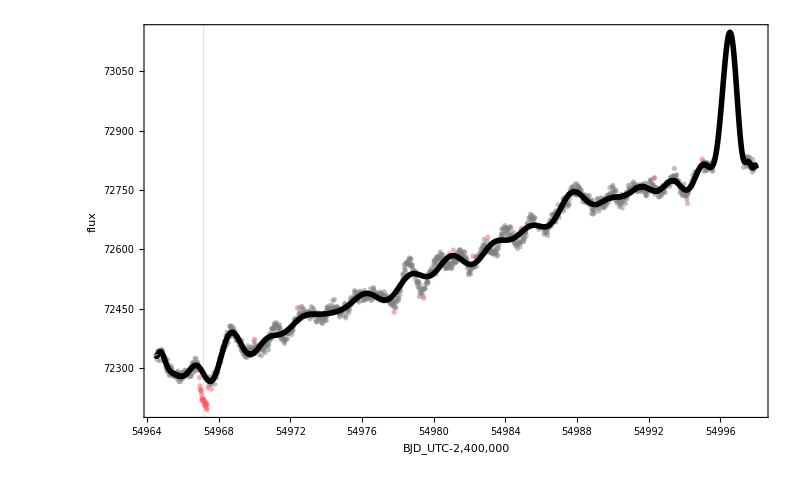

```mathematica
Qplot=Show[{ListPlot[{nicelist,missing},PlotStyle->{Directive[Gray,Opacity[0.5]],Directive[Lighter[Red],Opacity[0.5]]},Frame->True,FrameLabel->{"BJD_UTC-2,400,000","flux"},ImageSize->{800,550},BaseStyle->{FontFamily->"SF Pro Display",FontSize->24},Axes->None,PlotRange->{All,All}], 
 Plot[lmQ[t], {t, First[First[nicelist]], First[Last[nicelist]]},PlotStyle->{Black, Thickness[0.005]}]},Frame->True,Axes->None,GridLines->{{τ0+epoch Pp},{}},PlotRange->{All,All}]
```

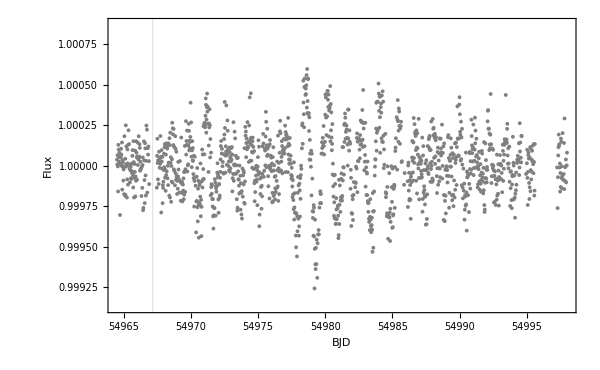

Standard deviation ~ 174.474 ppm

```mathematica
test=Table[lmQ[Extract[Extract[nice,i],1]],{i,1,Length[nice]}];
super=Table[{Extract[Extract[nice,i],1],Extract[Extract[nice,i],2]/Extract[test,i],Extract[Extract[nice,i],3]/Extract[test,i]},{i,1,Length[nice]}];
superlist=Table[{Extract[Extract[super,i],1],Extract[Extract[super,i],2]},{i,1,Length[super]}];
scatter=1.4286*Extract[MedianDeviation[super],2];
ListPlot[superlist,GridLines->{{τ0+epoch Pp},{}},Frame->True,BaseStyle->{"Times",16},FrameLabel->{"BJD","Flux"},ImageSize->{600,400},PlotStyle->{Gray},Axes->None,Joined->{False},PlotRange->{{First[First[superlist]],First[Last[superlist]]},{1-5*scatter,1+5*scatter}}]
Print["Standard deviation ~ ",scatter*10^6," ppm"]
```

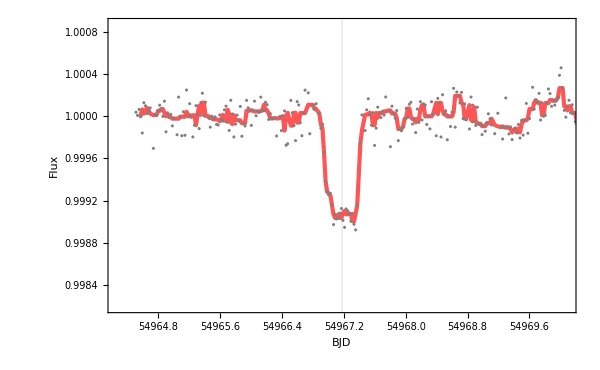

Standard deviation ~ 180.586 ppm

```mathematica
test2=Table[lmQ[Extract[Extract[err,i],1]],{i,1,Length[err]}];
gud=Table[{Extract[Extract[err,i],1],Extract[Extract[err,i],2]/Extract[test2,i],Extract[Extract[err,i],3]/Extract[test2,i]},{i,1,Length[err]}];
gudlist=Table[{Extract[Extract[gud,i],1],Extract[Extract[gud,i],2]},{i,1,Length[gud]}];
"START OF MIN FLUX ESTIMATOR";
j=0;m=0;Label[jloop];j=j+1;If[τ0+epoch Pp-0.25T14<Extract[Extract[gudlist,j],1]<τ0+epoch Pp+0.25T14,m=m+1];If[τ0+epoch Pp-0.25T14<Extract[Extract[gudlist,j],1]<τ0+epoch Pp+0.25T14,Subscript[μζ, m]=Extract[gudlist,j]];If[j<Length[gudlist],Goto[jloop]];
surround=Table[Subscript[μζ, mm],{mm,1,m}];surround=Table[{Extract[Extract[surround,i],1]-(τ0+epoch Pp),Extract[Extract[surround,i],2]},{i,1,Length[surround]}];
polyfit=NonlinearModelFit[surround,a+c t^2,{a,c},t];
minflux=polyfit[0];
"END OF MIN FLUX ESTIMATOR";
If[sc==0,smoothinteger=5,smoothinteger=30];
ListPlot[{gudlist,MovingMedian[gudlist,smoothinteger]},GridLines->{{τ0+epoch Pp},{}},Frame->True,BaseStyle->{"Times",16},FrameLabel->{"BJD","Flux"},ImageSize->{600,400},PlotStyle->{Gray,{Lighter[Red],Thickness[0.005]}},PlotRange->{{τ0+epoch Pp-2Thill,τ0+epoch Pp+2Thill},{minflux-5*scatter,1+5 scatter}},Axes->None,Joined->{False,True}]
Print["Standard deviation ~ ",1.4286*Extract[MedianDeviation[gud],2]*10^6," ppm"]
```

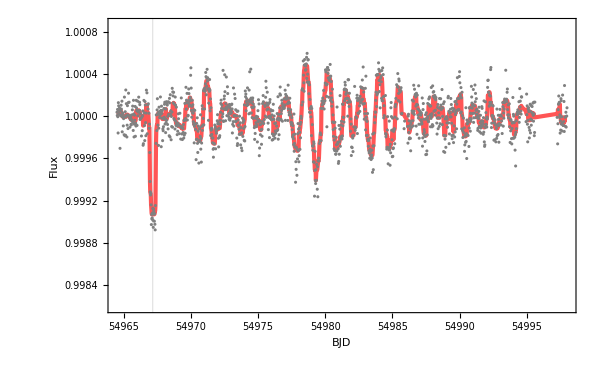

```mathematica
ListPlot[{gudlist,MovingMedian[gudlist,11]},GridLines->{{τ0+epoch Pp},{}},Frame->True,BaseStyle->{"Times",16},FrameLabel->{"BJD","Flux"},ImageSize->{600,400},PlotStyle->{Gray,{Lighter[Red],Thickness[0.005]}},PlotRange->{{First[First[gud]],First[Last[gud]]},{minflux-5*scatter,1+5 scatter}},Axes->None,Joined->{False,True}]
```

```mathematica
phase=Table[Extract[Extract[gud,i],1]-Pp Floor[(Extract[Extract[gud,i],1]-τ0)/Pp]-τ0,{i,1,Length[gud]}];
phase=Table[(Extract[phase,i]/Pp)-Round[(Extract[phase,i]/Pp)],{i,1,Length[phase]}];
j=0;m=0;Label[jloop];found=0;j=j+1;If[Abs[Extract[phase,j]]≤N[(2Thill)/Pp],found=1];If[found==1,m=m+1];If[found==1,Subscript[Δ, m]=Extract[gud,j]];If[j<Length[gud],Goto[jloop]];
m
```

254

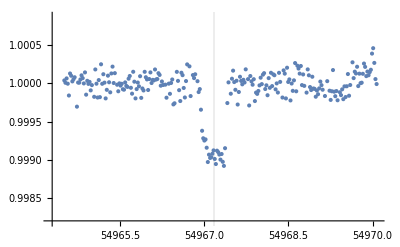

```mathematica
myQ=Table[Subscript[Δ, mm],{mm,1,m}];
myQlist=Table[{Extract[Extract[myQ,i],1],Extract[Extract[myQ,i],2]},{i,1,Length[myQ]}];
ListPlot[myQlist,PlotRange->{{τ0+epoch Pp-2Thill,τ0+epoch Pp+2Thill},{minflux-5*scatter,1+5 scatter}},GridLines->{{τ0+epoch Pp},{}}]
```

```mathematica
If[sc==0,bin=5,bin=30];
If[sc==0,sigma=100,sigma=3];
smoothfn=Interpolation[MovingMedian[myQlist,bin],InterpolationOrder->1];
res=Table[{Extract[Extract[myQ,i],1],Extract[Extract[myQ,i],2]-smoothfn[Extract[Extract[myQ,i],1]],Extract[Extract[myQ,i],3]},{i,1,Length[myQ]}];
j=0;m=0;Label[jloop];j=j+1;If[Abs[Extract[Extract[res,j],2]/Extract[Extract[res,j],3]]<sigma,m=m+1];If[Abs[Extract[Extract[res,j],2]/Extract[Extract[res,j],3]]<sigma,Subscript[γ, m]=Extract[myQ,j]];If[j<Length[res],Goto[jloop]];mmax=m;
myQ2=Table[Subscript[γ, mm],{mm,1,mmax}];
myQ2list=Table[{Extract[Extract[myQ2,i],1],Extract[Extract[myQ2,i],2]},{i,1,Length[myQ2]}];
Print[Length[myQ]-Length[myQ2]," points rejected"]
ListPlot[myQ2list,PlotRange->{{τ0+epoch Pp-2Thill,τ0+epoch Pp+2Thill},{minflux-5*scatter,1+5 scatter}},GridLines->{{τ0+epoch Pp},{}}]
```

InterpolatingFunction::dmval: Input value {54964.5} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {54970.1} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

0 points rejected

-Graphics-

```mathematica
phasex=Table[Extract[Extract[myQ2,i],1]-Pp Floor[(Extract[Extract[myQ2,i],1]-τ0)/Pp]-τ0,{i,1,Length[myQ2]}];
phasex=Table[(Extract[phasex,i]/Pp)-Round[(Extract[phasex,i]/Pp)],{i,1,Length[phasex]}];
```

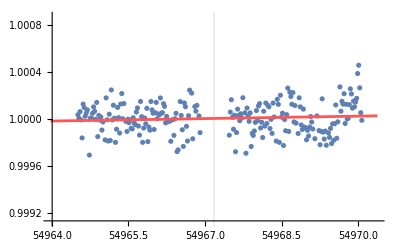

```mathematica
j=0;m=0;Label[jloop];found=0;j=j+1;If[N[gap/Pp]≤Abs[Extract[phasex,j]]≤N[(2Thill)/Pp],found=1];If[found==1,m=m+1];If[found==1,Subscript[φ, m]=Extract[myQ2,j]];If[j<Length[myQ2],Goto[jloop]];
baseQ=Table[Subscript[φ, mm],{mm,1,m}];
baseQlist=Table[{Extract[Extract[baseQ,i],1],Extract[Extract[baseQ,i],2]},{i,1,Length[baseQ]}];
linfit=LinearModelFit[baseQlist,x,x,Weights->Table[Extract[Extract[baseQ,i],3]^(-2),{i,1,Length[baseQ]}]];
Show[ListPlot[baseQlist,PlotRange->{{τ0+epoch Pp-2.2Thill,τ0+epoch Pp+2.2Thill},{1-5*scatter,1+5 scatter}},GridLines->{{τ0+epoch Pp},{}}],Plot[linfit[x],{x,τ0+epoch Pp-2.2Thill,τ0+epoch Pp+2.2Thill},PlotStyle->{Lighter[Red],Thickness[0.005]}]]
```

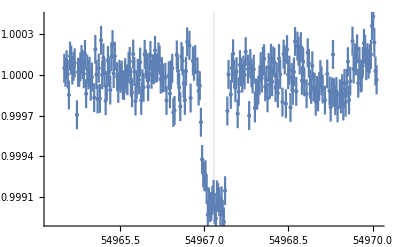

```mathematica
myQ3=Table[{Extract[Extract[myQ2,i],1],Extract[Extract[myQ2,i],2]/linfit[Extract[Extract[myQ2,i],1]],Extract[Extract[myQ2,i],3]/linfit[Extract[Extract[myQ2,i],1]]},{i,1,Length[myQ2]}];
<<ErrorBarPlots`
ErrorListPlot[myQ3,PlotRange->{{τ0+epoch Pp-2Thill,τ0+epoch Pp+2Thill},All},GridLines->{{τ0+epoch Pp},{}}]
```

```mathematica
"DURBIN-WATSONS...";
bin=30;jmax=Floor[N[Length[baseQ]/bin]];j=0;Label[jloop];j=j+1;tab=Table[Extract[baseQ,i],{i,(j-1)bin+1,j bin}];Subscript[ψΛ, j]={Sum[Extract[Extract[tab,i],1] Extract[Extract[tab,i],3]^-2,{i,1,Length[tab]}]/Sum[ Extract[Extract[tab,i],3]^-2,{i,1,Length[tab]}],Sum[Extract[Extract[tab,i],2] Extract[Extract[tab,i],3]^-2,{i,1,Length[tab]}]/Sum[ Extract[Extract[tab,i],3]^-2,{i,1,Length[tab]}]};If[j<jmax,Goto[jloop]];
If[sc==0,baseT=baseQ,baseT=Table[Subscript[ψΛ, jj],{jj,1,jmax}]];
baseTpre=Select[baseT,#[[1]]<τ0+epoch Pp&];baseTpost=Select[baseT,#[[1]]>τ0+epoch Pp&]; dwpre=Sum[(Extract[Extract[baseTpre,i],2]/linfit[Extract[Extract[baseTpre,i],1]]-Extract[Extract[baseTpre,i-1],2]/linfit[Extract[Extract[baseTpre,i-1],1]])^2,{i,2,Length[baseTpre]}]/Sum[(Extract[Extract[baseTpre,i],2]/linfit[Extract[Extract[baseTpre,i],1]]-1)^2,{i,2,Length[baseTpre]}];dwpost=Sum[(Extract[Extract[baseTpost,i],2]/linfit[Extract[Extract[baseTpost,i],1]]-Extract[Extract[baseTpost,i-1],2]/linfit[Extract[Extract[baseTpost,i-1],1]])^2,{i,2,Length[baseTpost]}]/Sum[(Extract[Extract[baseTpost,i],2]/linfit[Extract[Extract[baseTpost,i],1]]-1)^2,{i,2,Length[baseTpost]}];If[!NumberQ[dwpre],dwpre=2];If[!NumberQ[dwpost],dwpost=2];
dw=√((dwpre-2)^2+(dwpost-2)^2)
```

0.600392

```mathematica
chars=Characters[Last[StringSplit[NotebookFileName[],"/"]]]
letter=Extract[chars,First[First[Position[chars,"."]]]-1]
If[MemberQ[Alphabet[],letter],letter=StringJoin[letter,"."],letter="."]
If[pdc==1,file=StringJoin["cofiamPDC.",ToString[yy],".dat"],file=StringJoin["cofiamSAP.",ToString[yy],".dat"]];
If[Length[myQ]>0,Export[StringJoin[thisfolder,file],myQ3,"Table"],Print["No data"]]
```

{c,o,f,i,a,m,1,.,n,b}

1

.

/Users/dkipping/Storage1/Work/Documents/Transit_Work/PAPERS/Undersampled/LIGHTCURVES2/SINGLES/KOI-1888.01/planet1/SAP/cofiamSAP.1.dat

```mathematica
Speak["CoFiAM complete"]
```

```mathematica
If[Abs[Last[Subscript[ζζ, Last[First[results]]]]-0]<0.25,Speak["Good Durbin"],Speak[StringJoin["Caution, Durbin equals ",Table[Extract[Characters[ToString[Last[Subscript[ζζ, Last[First[results]]]]]],i],{i,1,4}]]]]
```